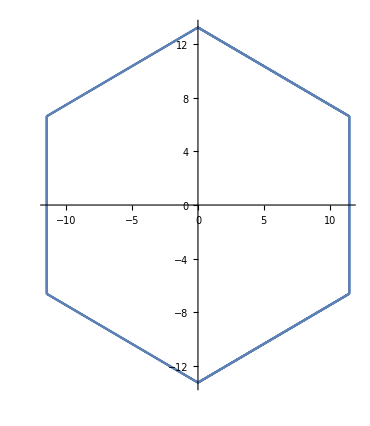

```mathematica
SpinMatrix[k1_,k2_,a_,ϵ1_,ϵ2_,t0_,t1_,t2_,t11_,t12_,t22_,λ_]:={{ϵ1+2*t0*(Cos[a*k1]+2*Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),2*t2*(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])+2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)],0,0,0},{-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),ϵ2+2*t11*Cos[a*k1]+(t11+3*t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)],Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])+λ*I,0,0,0},{2*t2(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])-2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)],Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])-λ*I,ϵ2+2*t22*Cos[a*k1]+(3*t11+t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)],0,0,0},{0,0,0,ϵ1+2*t0*(Cos[a*k1]+2*Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),2*t2*(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])+2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)]},{0,0,0,-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]), ϵ2+2*t11*Cos[a*k1]+(t11+3*t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)],Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])-λ*I},{0,0,0,2*t2(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])-2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)],Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])+λ*I,ϵ2+2*t22*Cos[a*k1]+(3*t11+t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)]}};

MasterHamiltonian[k1_,k2_,a_,ϵ1_,ϵ2_,t0_,t1_,t2_,t11_,t12_,t22_]:={{ϵ1+2*t0*(Cos[a*k1]+2*Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),2*t2*(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])+2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)]},{-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]), ϵ2+2*t11*Cos[a*k1]+(t11+3*t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)], Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+4*I*0.338*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])},{2*t2(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])-2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)], Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)]), ϵ2+2*t22*Cos[a*k1]+(3*t11+t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)]}};
a=.316;
(*a is the interatomic spacing, 3.16  Angstroms is its actual value*)
R=4*Pi/(3a);
f=Interpolation[Table[{a,R {Cos[a],Sin[a]}},{a,-Pi/2-2*π,Pi/2+2*π,π/3}],InterpolationOrder->1];
ParametricPlot[f[a],{a,-Pi/2-2*π,+Pi/2+2*π}]
```

```mathematica
Plot3D[Sort[Re[Eigenvalues[SpinMatrix[kx,ky,0.3326,0.919,2.065,-0.188,0.317,0.456,0.211,0.290,0.130,0.073]]]],{kx,-R,R},{ky,-R,R},AspectRatio->1.25,RegionFunction->Function[{x,y,z},Norm[{x,y}]≤Norm[f[ArcTan[y,x]]]],AxesLabel->{kx,ky,Energy}]
(*Dispersion relation for Mos2 with the correction to spin added*)
```

-Graphics3D-

```mathematica
(*Dispersion relation of WS2 with the spin correction*)
Plot3D[Sort[Re[Eigenvalues[SpinMatrix[kx,ky,0.3191,1.130,2.275,-0.206,0.567,0.536,0.286,0.384,-0.061,0.211]]]],{kx,-R,R},{ky,-R,R},AspectRatio->1.25,RegionFunction->Function[{x,y,z},Norm[{x,y}]≤Norm[f[ArcTan[y,x]]]],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

```mathematica
(*Dispersion relation for MoSe2 with the spin correction*)
Plot3D[Sort[Re[Eigenvalues[SpinMatrix[kx,ky,0.3326,0.919,2.065,-0.188,0.317,0.456,0.211,0.290,0.130,0.091]]]],{kx,-R,R},{ky,-R,R},AspectRatio->1.25,RegionFunction->Function[{x,y,z},Norm[{x,y}]≤Norm[f[ArcTan[y,x]]]],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

```mathematica
(*Dispersion relation for WSe2 with the spin correction*)
Plot3D[Sort[Re[Eigenvalues[SpinMatrix[kx,ky,0.3236,0.919,2.065,-0.188,0.317,0.456,0.211,0.290,0.120,0.228]]]],{kx,-R,R},{ky,-R,R},AspectRatio->1.25,RegionFunction->Function[{x,y,z},Norm[{x,y}]≤Norm[f[ArcTan[y,x]]]],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

```mathematica
(*Band diagram plotted over the line where kx=0, ky runs from -R to R*)
Plot[Sort[Re[Eigenvalues[SpinMatrix[0,ky,0.3326,0.919,2.065,-0.188,0.317,0.456,0.211,0.290,0.130,0.073]]]],{ky,-R,R}]
```

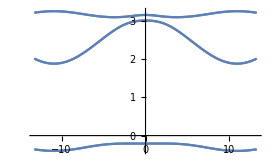

```mathematica
(*Band diagram plotted over the top boundary of the hexagon*)
Plot[Sort[Re[Eigenvalues[SpinMatrix[kx,11.4,0.3326,0.919,2.065,-0.188,0.317,0.456,0.211,0.290,0.130,0.073]]]],{kx,-R,R}]
```

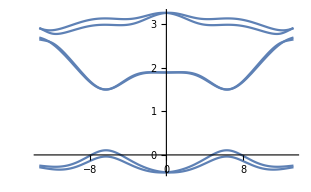

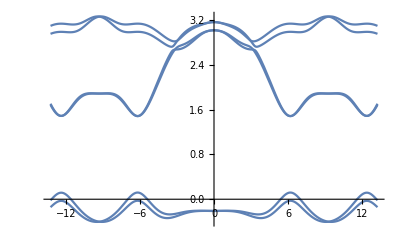

```mathematica
(*Band diagram plotted over the line running from the center of the hexagon out to the top right hand corner*)
Plot[Sort[Re[Eigenvalues[SpinMatrix[kx,1.77kx,0.3326,0.919,2.065,-0.188,0.317,0.456,0.211,0.290,0.130,0.073]]]],{kx,-R,R}]
```